```mathematica
ClearAll["Global`*"]
$Assumptions=A∈Integers&&A>2&&α∈Reals&&α>0&&λ∈Reals&&λ>0&&β∈Reals&&β>0&&R∈Reals&&Rp∈Reals;
```

system parameter:
A (int) : total number of particles
F (int) : number of fragments
Z (int array) : number of particles in fragments
d (int) : number of spatial dimensions (ECCE: do not use; from the 1-dim result, one should be able to deduce the d-dim variant)

```mathematica
A=4;
F=2;
Z={2,2};
If[Total[Z]!=A||Dimensions[Z][[1]]!=F,Print["System definition erroneous."]]
```

coordinate transformations:
single-particle   →  cluster-relative : T
cluster-relative  →  single-particle  : T^-1

```mathematica
SingleToCluster={};
For[f=1,f≤F,f++,{
For[i=1,i≤Z[[f]]-1,i++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+1]],0,j==Prepend[Accumulate[Z],0][[f]]+i,(Z[[f]]-1)/Z[[f]],1==1,-1/Z[[f]]],{j,1,A}]
]
}];
}];
For[f=1,f<F,f++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+2]],0,j<=Prepend[Accumulate[Z],0][[f+1]],1/Z[[f]],1==1,-1/Z[[f+1]]],{j,1,A}]
]
}];
AppendTo[SingleToCluster,
Table[1/A,{j,1,A}]
];
Single=Array[Subscript["r⃗", ##]&,{A}];
Cluster=Flatten[Table[Array[Subscript["r̄", Prepend[Accumulate[Z],0][[f]]+##]&,{Z[[f]]-1}],{f,F}]];
AppendTo[Cluster,ArrayFlatten[Array[Subscript["R⃗", ##]&,{F-1}],1][[1]]];AppendTo[Cluster,"(R⃗)_cm"];
Tmat=SingleToCluster;
Tmatinv=Inverse[SingleToCluster];
TproR=Table[If[(m==A-1),Tmat[[m,n]],0],{m,A},{n,A}];
Print[Cluster//MatrixForm,"=",SingleToCluster//MatrixForm,"·",Single//MatrixForm]
Print[Cluster//MatrixForm,"=",TproR//MatrixForm,"·",Single//MatrixForm]
```

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(1/2 | -1/2 | 0 | 0
0 | 0 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2
1/4 | 1/4 | 1/4 | 1/4)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 0)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

quadratic form of fragment wave functions in cluster-relative coordinates:

```mathematica
Wmat={};
For[f=1,f≤F,f++,(
AppendTo[Wmat,Table[If[pos==f,Table[If[m==n,4 Subscript[a, f],2 Subscript[a, f]],{n,Z[[f]]-1},{m,Z[[f]]-1}],0],{pos,F}]];
)];
Wmat=Table[If[(m>A-2)||(n>A-2),0,ArrayFlatten[Wmat][[n]][[m]]],{n,A},{m,A}];
Print[Wmat//MatrixForm]
```

(4 a_1 | 0 | 0 | 0
0 | 4 a_2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

matrix representation of the permutation (single-particle coordinates):
(a | b | ... | A
p(a) | p(b) | ... | p(A))   original order
permuted order      ⇒    p(a)-th row→(⋮
a
⋮)=(□ | □ | □
□ | □ | □
□ | □ | □)·(a
⋮
A)
Pij[ i,j ] = Perm[ {{i,j},{j,i}} ]

```mathematica
Pij[i_,j_]:=Table[If[((r==i)&&(c==j))||((r==j)&&(c==i))||((r≠i)&&(c≠j)&&(c==r)),1,0],{r,1,A},{c,1,A}];
Perm[ord_]:=
Module[{},
pmat=IdentityMatrix[A];
Do[
pmat[[move[[1]],move[[1]]]]=0;
pmat[[move[[2]],move[[1]]]]=1;
,{move,ord}];
If[(Total[pmat,{1}]==ConstantArray[1,A])&&(Total[pmat,{2}]==ConstantArray[1,A]),
pmat,Print["illdefined permutation!"]]
];
```

quadratic form of a two-body Gaussian interaction in cluster-relative coordinates:
V_(F_1 F_2)=∑_((i∈F_1)_(j∈F_2)) e^(-(λ(r_i-r_j))^2)

```mathematica
Pv[i_,j_]:=Table[If[(n==m==j)||(n==m==i),1,0],{n,A},{m,A}];
Vr[i_,j_]:=If[i≠j,Table[Which[((n==m==i))||((n==m==(j))),2 λ,((n==i)&&(m==j))||((m==i)&&(n==j)),-2 λ,1==1,0],{n,A},{m,A}],Table[0,{n,A},{m,A}]];
Vij[i_,j_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j].Pv[i,j].Tmatinv;
Vijk[i_,j_,k_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j].Pv[i,j].Tmatinv+Transpose[Pv[i,k].Tmatinv].Vr[i,k].Pv[i,k].Tmatinv;
```

full quadratic form of a two-body Gaussian interaction between i,j and a permutation of particles m,n (matrix representation in cluster-relative coordinates):
dimer-dimer w/o discrete scale invariance:  V=δ_13+δ_23+δ_24+δ_234+δ_123    A=OverHat[1]-P_14

```mathematica
ivtest=1;jvtest=3;kvtest=ivtest;
testperm={};
Wfull[iv_,jv_,kv_,permu_]:=Wmat+Vijk[iv,jv,kv]+Transpose[(Tmat.Perm[permu].Tmatinv)].Wmat.(Tmat.Perm[permu].Tmatinv);
Sfull[permu_]:=TproR.Perm[permu].Tmatinv;
Amat[iv_,jv_,kv_,permu_]:=Wfull[iv,jv,kv,permu][[1;;(A-2),1;;(A-2)]];
S3[Rp_,s_,iv_,jv_,kv_,permu_]:=-Rp Wfull[iv,jv,kv,permu][[A-1,1;;A-2]]-I s Sfull[permu][[A-1,1;;A-2]];
S4[s_,permu_]:=-I s Sfull[permu][[A-1,A-1]];
M1[iv_,jv_,kv_,permu_]:=Wfull[iv,jv,kv,permu][[A-1,A-1]];
Print["W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = ",Wfull[ivtest,jvtest,kvtest,testperm]//MatrixForm,"         (S̲)_full = T_RPT^-1 = ",Sfull[testperm]//MatrixForm,"         (V̲)_ij = ",Vij[ivtest,jvtest]//MatrixForm,"         (V̲)_ijk = ",Vijk[ivtest,jvtest,kvtest]//MatrixForm]
Print["         A̲ = ",Amat[ivtest,jvtest,kvtest,testperm]//MatrixForm,"         (A̲)^-1 = ",Simplify[Inverse[Amat[ivtest,jvtest,kvtest,testperm]]]//MatrixForm,"         S_3 = ",S3[Rp,s,ivtest,jvtest,kvtest,testperm]//MatrixForm,"         S_4 = ",S4[s,testperm]//MatrixForm,"         M_1 = ",M1[ivtest,jvtest,kvtest,testperm]//MatrixForm]
```

W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = (2 λ+8 a_1 | -2 λ | 2 λ | 0
-2 λ | 2 λ+8 a_2 | -2 λ | 0
2 λ | -2 λ | 2 λ | 0
0 | 0 | 0 | 0)         (S̲)_full = T_RPT^-1 = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)         (V̲)_ij = (2 λ | -2 λ | 2 λ | 0
-2 λ | 2 λ | -2 λ | 0
2 λ | -2 λ | 2 λ | 0
0 | 0 | 0 | 0)         (V̲)_ijk = (2 λ | -2 λ | 2 λ | 0
-2 λ | 2 λ | -2 λ | 0
2 λ | -2 λ | 2 λ | 0
0 | 0 | 0 | 0)

A̲ = (2 λ+8 a_1 | -2 λ
-2 λ | 2 λ+8 a_2)         (A̲)^-1 = ((λ+4 a_2)/(8 (λ a_2+a_1 (λ+4 a_2))) | λ/(8 (λ a_2+a_1 (λ+4 a_2)))
λ/(8 (λ a_2+a_1 (λ+4 a_2))) | (λ+4 a_1)/(8 (λ a_2+a_1 (λ+4 a_2))))         S_3 = (-2 Rp λ
2 Rp λ)         S_4 = -ⅈ s         M_1 = 2 λ

r̄ - integration

```mathematica
scoeff[Rp_,Rpp_,iv_,jv_,kv_,permu_]:=CoefficientList[Simplify[1/2 S3[Rp,s,iv,jv,kv,permu].Inverse[Amat[iv,jv,kv,permu]].S3[Rp,s,iv,jv,kv,permu]-1/2 Rp M1[iv,jv,kv,permu] Rp+S4[s,permu] Rp+I s Rpp],s];
S5[Rp_,Rpp_,iv_,jv_,kv_,permu_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu][[2]]];
S6[Rp_,Rpp_,iv_,jv_,kv_,permu_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu][[1]]];
Kmat[Rp_,Rpp_,iv_,jv_,kv_,permu_]:=
If[Length[scoeff]<3,
0
,
-2 Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu][[3]]]
];
Kmatinv[Rp_,Rpp_,iv_,jv_,kv_,permu_]:=If[Kmat[Rp,Rpp,iv,jv,kv,permu]==0,
0
,
1/Kmat[Rp,Rpp,iv,jv,kv,permu]
];

Print[S6[Rp,Rpp,ivtest,jvtest,kvtest,testperm]," + ",S5[Rp,Rpp,ivtest,jvtest,kvtest,testperm],"s  +",Kmat[Rp,Rpp,ivtest,jvtest,kvtest,testperm],"s^2"]
```

-(4 Rp^2 λ a_1 a_2)/(λ a_2+a_1 (λ+4 a_2)) + -ⅈ (Rp-Rpp)s  +0s^2

s - integration

(T̂-E)_direct                                                                            :  λ=0  ,  i_p=j_p                  ⇒P̂=𝟙
δ_13^X (no scale invariance (ab)-(ca) dimer-dimer)  :  λ=Λ ,  i_p=1 ,j_p=4 ⇒(P̂)_14

```mathematica
genericRGMEQcomponent[R_,Rp_,a1_,a2_,lec_,lam_,scale_,ii_,jj_,kk_,permu_]:=Module[{},
kin=(lam==0);

Rcoeff=CoefficientList[
1/2 S5[R,Rp,ii,jj,kk,permu] Kmatinv[R,Rp,ii,jj,kk,permu] S5[R,Rp,ii,jj,kk,permu]+S6[R,Rp,ii,jj,kk,permu]
,Rp];

αR=Simplify[Rcoeff[[1]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,λ->lam}];

If[Length[Rcoeff]>1,αRRp=Simplify[Rcoeff[[2]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,λ->lam}],αRRp=0];
If[Length[Rcoeff]==3,αRp=Simplify[Rcoeff[[3]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,λ->lam}],αRp=0];

detA=Simplify[Det[Amat[ii,jj,kk,permu]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,λ->lam}];
detK=If[Kmat[R,Rp,ii,jj,kk,permu]==0,1,Simplify[Kmat[R,Rp,ii,jj,kk,permu]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,λ->lam}]];
If[kin,lec=1,0];

strength=Simplify[lec Sqrt[(2 Pi)/(detA detK)]];

strength Exp[αR]Exp[αRp Rp^2] Exp[αRRp Rp]
];
```

```mathematica
a=α;b=α;
scaleexponent=0;
lamba=Λ;
ivtest=2;jvtest=3;kvtest=2;
testperm={{1,4},{4,1}};
genericRGMEQcomponent["r","r̃",a,b,Subscript[C, LEC],lamba,scaleexponent,ivtest,jvtest,kvtest,testperm]
```

1/4 ⅇ^(-(r^2 α (α+2 Λ))/(α+Λ)) √π √(1/(α^2+α Λ)) C_LEC

## Dimer-Dimer (AB)-(CA) (scale variant with 3-body forces)

V_(ab-ca)=C_0(δ_13+δ_23+δ_24)+D_1(δ_234+δ_123)  ;  A=𝟙-P_14
RGM equation:     ⟨ϕ_A ϕ_B|(T̂-E+V)|Â [ϕ_A ϕ_B χ(R)]⟩=0
avg. ⟨...⟩ over fragment-internal coordinates;       R: inter-fragment  separation

```mathematica
p14={{1,4},{4,1}};
Vdi3bdy[r_,rp_,omegadimer_,d0_,lambda_,sc3_]:=(genericRGMEQcomponent[x,y,α,α,d0,Λ,sc3,1,2,3,{}]+genericRGMEQcomponent[x,y,α,α,d0,Λ,sc3,4,3,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vdi2bdy[r_,rp_,omegadimer_,c0_,lambda_,sc2_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,3,2,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,1,3,1,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,4,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vex3bdy[r_,rp_,omegadimer_,d0_,lambda_,sc3_]:=(genericRGMEQcomponent[x,y,α,α,d0,Λ,sc3,1,2,3,p14]+genericRGMEQcomponent[x,y,α,α,d0,Λ,sc3,4,3,2,p14])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vex2bdy[r_,rp_,omegadimer_,c0_,lambda_,sc2_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,3,2,p14]+genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,1,3,1,p14]+genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,4,2,p14])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vcomplete[r_,rp_,omegadimer_,lambda_,c0_,d0_,sc2_,sc3_]:=(Vdi2bdy[r,rp,omegadimer,c0,lambda,sc2]+Vdi3bdy[r,rp,omegadimer,d0,lambda,sc3])-(Vex2bdy[r,rp,omegadimer,c0,lambda,sc2]+Vex3bdy[r,rp,omegadimer,d0,lambda,sc3]);
```

V_(ab-ca)=C_0(δ_13+δ_23+δ_24)+D_1(δ_234+δ_123)  ;  A=𝟙-P_14
RGM equation:     ⟨ϕ_A ϕ_B|V_(ab-ca)|Â [ϕ_A ϕ_B χ(R)]⟩=0

```mathematica
Clear[Λ];
Simplify[Vcomplete["r","r̃",α,Λ,Subscript[C, 0],Subscript[D, 1],Subscript[n, 2],Subscript[n, 3]]]
```

1/4 √π ((-ⅇ^(-(r^2 α (α+2 Λ))/(α+Λ)) √(1/(α^2+α Λ))+3 ⅇ^(-(2 r^2 α Λ)/(2 α+Λ)) √(1/(2 α^2+α Λ))-2 √2 ⅇ^(-(r^2 α (2 α+3 Λ))/(2 α+Λ)) √(1/(2 α^2+α Λ))) C_0+2 √2 (-ⅇ^(-(2 r^2 α (α^2+3 α Λ+2 Λ^2))/(2 α^2+4 α Λ+Λ^2)) √(1/(2 α^2+4 α Λ+Λ^2))+ⅇ^(-(4 r^2 α Λ (α+Λ))/(4 α^2+6 α Λ+Λ^2)) √(1/(4 α^2+6 α Λ+Λ^2))) D_1)

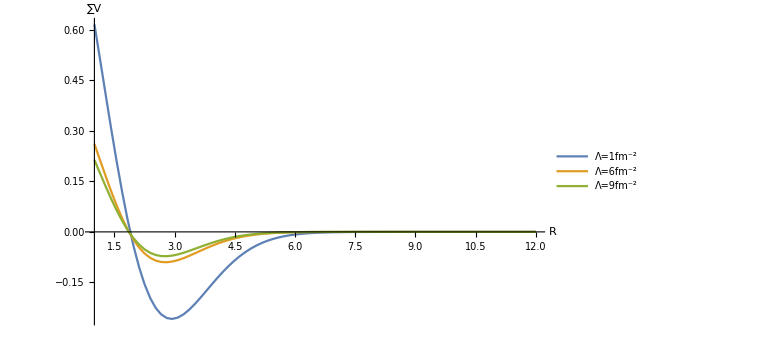

```mathematica
Rmax=12.0;y0=0.015;alpha=0.1;lambda=4;n2=2;n3=4;c0=-1;d0=1;

lambdas={1,6,9};
Plot[Evaluate@Table[Vcomplete[r,y0,alpha,lambda,c0,d0,n2,n3],{lambda,lambdas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large]
```

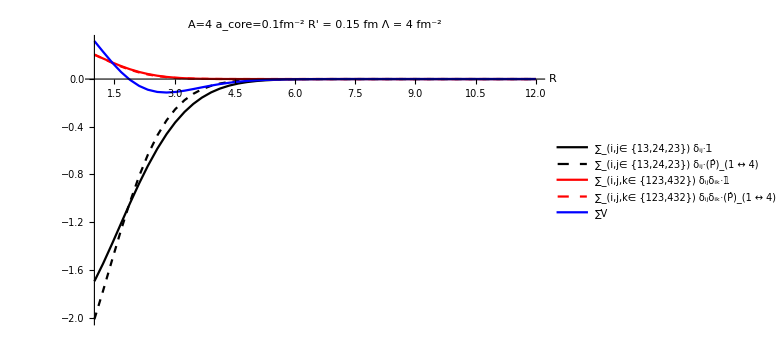
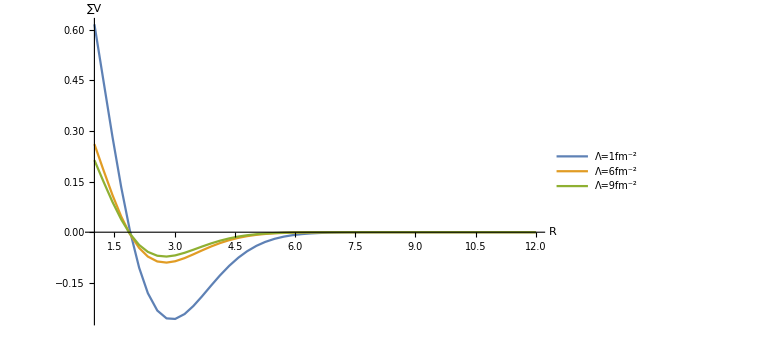
-Graphics- | -Graphics-

```mathematica
Grid[{{
Plot[Evaluate@{Vdi2bdy[r,y0,alpha,c0,lambda,n2],Vex2bdy[r,y0,alpha,c0,lambda,n2],Vdi3bdy[r,y0,alpha,d0,lambda,n3],Vex3bdy[r,y0,alpha,d0,lambda,n3],Vcomplete[r,y0,alpha,lambda,c0,d0,n2,n3]},{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,PlotLabel->"A="<>ToString[A]<>"   a_core="<>ToString[alpha]<>"fm^-2"<>"  R' = "<>ToString[y0]<>" fm    Λ = "<>ToString[lambda]<>" fm^-2",PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed},{Blue,Thick}},AxesLabel->{"R"},PlotLegends->{"∑_(i,j∈
{13,24,23}) δ_ij·𝟙","∑_(i,j∈
{13,24,23}) δ_ij·(P̂)_(1 ↔ 4)","∑_(i,j,k∈
{123,432}) δ_ijδ_ik·𝟙","∑_(i,j,k∈
{123,432}) δ_ijδ_ik·(P̂)_(1 ↔ 4)","∑V"},PlotRange->Full,ImageSize->Large],
Plot[Evaluate@Table[Vcomplete[r,y0,alpha,lambda,c0,d0,n2,n3],{lambda,lambdas}],{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large]
}}]
```

## Dimer-Dimer (AB)-(AB) (scale invariant, 2-body forces only)

V_(ab-ab)=C_0(δ_13+δ_24)  ;  A=𝟙-P_14-P_23+P_14 P_23
RGM equation:     ⟨ϕ_A ϕ_B|(T̂-E+V)|Â [ϕ_A ϕ_B χ(R)]⟩=0
avg. ⟨...⟩ over fragment-internal coordinates;       R: inter-fragment  separation

```mathematica
p23={{2,3},{3,2}};p14p23={{1,4},{4,1},{2,3},{3,2}};
iVdi2bdy[r_,rp_,omegadimer_,c0_,lambda_,sc2_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,1,3,1,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,4,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
iVex2bdy[r_,rp_,omegadimer_,c0_,lambda_,sc2_]:=(-genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,1,3,1,p14]-genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,4,2,p14]-genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,1,3,1,p23]-genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,4,2,p23]+
genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,1,3,1,p14p23]+
genericRGMEQcomponent[x,y,α,α,c0,Λ,sc2,2,4,2,p14p23]
)/.{x->r,y->rp,α->omegadimer,Λ->lambda};
iVcomplete[r_,rp_,omegadimer_,lambda_,c0_,sc2_]:=iVdi2bdy[r,rp,omegadimer,c0,lambda,sc2]+iVex2bdy[r,rp,omegadimer,c0,lambda,sc2];
```

V_(ab-ab)=C_0(δ_13+δ_24)  ;  A=𝟙-P_14-P_23+P_14 P_23
RGM equation:     ⟨ϕ_A ϕ_B|V_(ab-ab)|Â [ϕ_A ϕ_B χ(R)]⟩=0

```mathematica
Clear[Λ];
Simplify[iVcomplete["r","r̃",α,Λ,Subscript[C, 0],Subscript[n, 2]]]
```

1/4 (4 ⅇ^(-(2 r^2 α Λ)/(2 α+Λ))-3 √2 ⅇ^(-(r^2 α (2 α+3 Λ))/(2 α+Λ))) √π √(1/(2 α^2+α Λ)) C_0

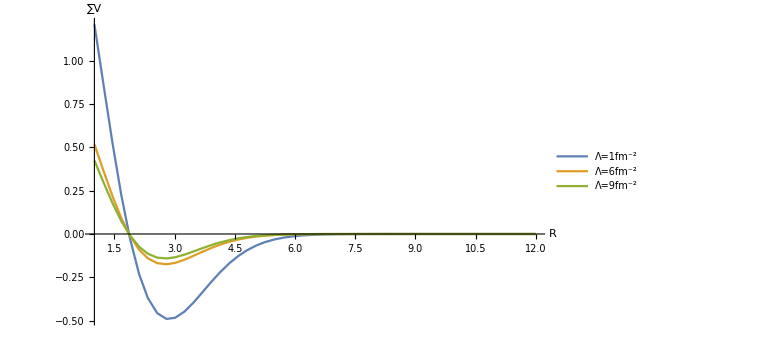

```mathematica
Rmax=12.0;y0=0.15;alpha=0.1;lambda=4;n2=2;c0=-1;

lambdas={1,6,9};
Plot[Evaluate@Table[iVcomplete[r,y0,alpha,lambda,c0,n2],{lambda,lambdas}],{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large]
```

## Predictions: Dimer-Dimer

```mathematica
ScatteringLength[v0_?NumberQ]:=Block[{f,w},f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 v[c0,r]==0,w[0]==10^20},w,{r,0,R}][[1,1]]];R-f[R]^-1]
```